### Create a state equation using MMS.

```mathematica
A=-{{1,0},{1,2}}
```

(-1 | 0
-1 | -2)

Pick a “seed” function to generate the forcing function b(t). IMPORTANT: this will not (usually) be the solution to the optimization problem, because in the optimization setting we’re free to choose initial values to get a better fit to the target.

```mathematica
Subscript[x, seed][t_]={ (1/2+t^2)Exp[-t], (1/3+t) Exp[-2t] }
```

{ⅇ^-t (t^2+1/2),ⅇ^(-2 t) (t+1/3)}

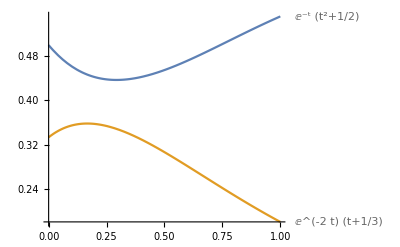

```mathematica
Plot[{Subscript[x, seed][t][[1]],Subscript[x, seed][t][[2]]},{t,0,1},PlotLabels->{Subscript[x, seed][t][[1]],Subscript[x, seed][t][[2]]}]
```

Create the RHS function b(t)

```mathematica
b[t_]=Subscript[x, seed]'[t]-A.Subscript[x, seed][t]
```

{2 ⅇ^-t t,ⅇ^-t (t^2+1/2)+ⅇ^(-2 t)}

#### Use DSolve to produce the general solution to the ODE we’ve manufactured

```mathematica
X[t_]={Subscript[x, 1][t],Subscript[x, 2][t]}
```

{x_1(t),x_2(t)}

Solve using parameters α and β as the initial conditions.

```mathematica
xSoln[α_,β_,t_]=X[t]/.DSolve[{X'[t]==A.X[t]+b[t],X[0]=={α,β}},X[t],t][[1]]//FullSimplify
```

{ⅇ^-t (α+t^2),1/2 ⅇ^(-2 t) (2 α+2 β+(1-2 α) ⅇ^t+2 t-1)}

Sanity check: make sure we recover the seed function when we use x_seed[0] as the ICs

```mathematica
FullSimplify[xSoln[Subscript[x, seed][0][[1]],Subscript[x, seed][0][[2]],t]==Subscript[x, seed][t]]
```

True

### Pick a target function

I’ll choose a target that’s a perturbation of the seed function, parametrized by γ. When γ=0 we get back the seed function.

```mathematica
SuperStar[x][γ_,t_]=Subscript[x, seed][t] + γ {t(t-1/2),(t-3/4)/5}
```

{ⅇ^-t (t^2+1/2)+γ (t-1/2) t,1/5 γ (t-3/4)+ⅇ^(-2 t) (t+1/3)}

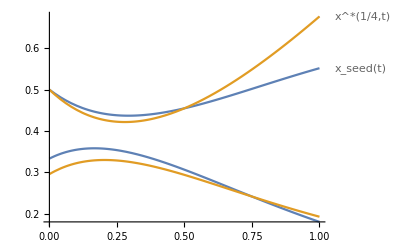

```mathematica
Plot[{Subscript[x, seed][t],SuperStar[x][1/4,t]},{t,0,1},PlotLabels->Automatic]
```

### Set up the objective function

Integrand: square the difference between a solution to the ODE (given ICs α and β) and the target.

```mathematica
F[α_,β_,γ_,t_]=(xSoln[α,β,t]-SuperStar[x][γ,t]).(xSoln[α,β,t]-SuperStar[x][γ,t])
```

(ⅇ^-t (α+t^2)-ⅇ^-t (t^2+1/2)-γ (t-1/2) t)^2+(1/2 ⅇ^(-2 t) (2 α+2 β+(1-2 α) ⅇ^t+2 t-1)-1/5 γ (t-3/4)-ⅇ^(-2 t) (t+1/3))^2

Integrate to compute the objective function

```mathematica
f[α_,β_,γ_]=1/2 Integrate[F[α,β,γ,t],{t,0,1}]//FullSimplify
```

1/(7200 ⅇ^4)(ⅇ^4 (2100 α^2-20 α (30 β+513 γ+95)+30 (6 β+169) γ+75 (4 β (3 β-1)+7)+141 γ^2)+90 ⅇ^2 (6 γ (α+β)-40 (α-1) α-5 (γ+2))-25 (6 α+6 β-5)^2+200 ⅇ (2 α-1) (6 α+6 β-5)+13500 ⅇ^3 (2 α-1) γ)

### Minimize

Set the gradient of f to zero

```mathematica
minCond[γ_]=({D[f[α,β,γ],α],D[f[α,β,γ],β]}//FullSimplify)=={0,0}
```

{(ⅇ (5 ⅇ (ⅇ^2 (42 α-6 β-19)-72 α+36)+40 (6 α+3 β-4)+27 ⅇ (1+(50-19 ⅇ) ⅇ) γ)-15 (6 α+6 β-5))/(360 ⅇ^4),(ⅇ (ⅇ^3 (-10 α+30 β+3 γ-5)+40 α+9 ⅇ γ-20)-5 (6 α+6 β-5))/(120 ⅇ^4)}=={0,0}

```mathematica
minSoln[γ_]:={α,β}/.Solve[minCond[γ],{α,β}][[1]]
```

Here’s the solution as a function of γ. (The symbolic expression is enormous)

```mathematica
Simplify[minSoln[γ]//N]
```

{0.0550306 γ+0.5,0.333333-0.127233 γ}

### Export problem info to C

```mathematica
CForm[A//N]
```

List(List(-1.,0.),List(-1.,-2.))

```mathematica
CForm[Transpose[A//N]]
```

List(List(-1.,-1.),List(0.,-2.))

```mathematica
CForm[b[t]]
```

List((2*t)/Power(E,t),
   Power(E,-2*t) + (0.5 + Power(t,2))/Power(E,t))

```mathematica
CForm[SuperStar[x][γ,t]]
```

List((0.5 + Power(t,2))/Power(E,t) + 
    (-0.5 + t)*t*γ,(0.3333333333333333 + t)/
     Power(E,2*t) + ((-0.75 + t)*γ)/5.)

```mathematica
CForm[Simplify[minSoln[γ]//N]]
```

List(0.49999999999999994 + 0.05503059750329588*γ,
   0.3333333333333333 - 0.1272325603758784*γ)